```mathematica
BeginPackage["Optimise`ParticleSwarm`"];
```

```mathematica
ParticleSwarm::usage="ParticleSwarm[Objective Function, No Of Chromosomes, Iterations, Genes per Chrom., Start of range, End of range]\nParticleSwarm is a MAXIMISING Function!";
```

```mathematica
ParticleSwarmComplex::usage="ParticleSwarm[Objective Function, No Of Chromosomes, Iterations, Genes per Chrom., Start of range, End of range]\nParticleSwarm is a MAXIMISING Function!";
```

```mathematica
ParticleSwarm::Options="ParticleSwarm supports 5 possible options: SelectionMethod, BreedingPool, ReinsertionMethod, BreedingRate, MutationRate;\nSee EPOptimiseReal[<Option Name>];"
```

ParticleSwarm supports 5 possible options: SelectionMethod, BreedingPool, ReinsertionMethod, BreedingRate, MutationRate;
See EPOptimiseReal[<Option Name>];

```mathematica
ParticleSwarm::SelectionMethod="SelectionMethod specifies one of 4 methods for selecting the possible breeding population.\nThe options are:\nRoulette\nUniversal\nTruncation\nTournament"
```

SelectionMethod specifies one of 4 methods for selecting the possible breeding population.
The options are:
Roulette
Universal
Truncation
Tournament

```mathematica
ParticleSwarm::Roulette="In the Roulette SelectionMethod The individuals are mapped to contiguous segments of a line, such that each individual's segment is equal in size to its fitness. A random number is generated and the individual whose segment spans the random number is selected. This is repeated to select the breeding population required."
```

In the Roulette SelectionMethod The individuals are mapped to contiguous segments of a line, such that each individual's segment is equal in size to its fitness. A random number is generated and the individual whose segment spans the random number is selected. This is repeated to select the breeding population required.

```mathematica
ParticleSwarm::Universal="In the Universal SelectionMethod the individuals are mapped to contiguous segments of a line, such that each individual's segment is equal in size to its fitness exactly as in Roulette selection. Here equally spaced pointers are placed over the line as many as there are individuals to be selected, and the breeding population thus chosen."
```

In the Universal SelectionMethod the individuals are mapped to contiguous segments of a line, such that each individual's segment is equal in size to its fitness exactly as in Roulette selection. Here equally spaced pointers are placed over the line as many as there are individuals to be selected, and the breeding population thus chosen.

```mathematica
ParticleSwarm::Truncation="In Truncation selection individuals are sorted according to their fitness. Only the best individuals are selected for parents. The parameter for truncation selection is the TruncationThreshold. TruncationThreshold indicates the proportion of the population to be selected as parents and takes values ranging from 50%-10%. Individuals below the truncation threshold do not produce offspring."
```

In Truncation selection individuals are sorted according to their fitness. Only the best individuals are selected for parents. The parameter for truncation selection is the TruncationThreshold. TruncationThreshold indicates the proportion of the population to be selected as parents and takes values ranging from 50%-10%. Individuals below the truncation threshold do not produce offspring.

```mathematica
ParticleSwarm::TruncationThreshold="TruncationThreshold indicates the proportion of the population to be selected as parents in the Truncation SelectionMethod, and takes values ranging from 50%-10%."
```

TruncationThreshold indicates the proportion of the population to be selected as parents in the Truncation SelectionMethod, and takes values ranging from 50%-10%.

```mathematica
ParticleSwarm::Tournament="In Tournament selection a number TournamentNumber of individuals is chosen randomly from the population and the best individual from this group is selected as a parent. This process is repeated as often as individuals must be chosen."
```

In Tournament selection a number TournamentNumber of individuals is chosen randomly from the population and the best individual from this group is selected as a parent. This process is repeated as often as individuals must be chosen.

```mathematica
ParticleSwarm::TournamentNumber="TournamentNumber is the number of individuals to be tested in each tournament round in the Tournament SelectionMethod."
```

TournamentNumber is the number of individuals to be tested in each tournament round in the Tournament SelectionMethod.

```mathematica
ParticleSwarm::BreedingPool="The BreedingPool is the size of the breeding population at each iteration. This is the total possible breeding population, and not all individuals chosen will breed. See EPOptimiseReal[Breeding]."
```

The BreedingPool is the size of the breeding population at each iteration. This is the total possible breeding population, and not all individuals chosen will breed. See EPOptimiseReal[Breeding].

```mathematica
ParticleSwarm::Breeding="When breeding individuals, the breeding population is chosen using the SelectionMethod variable and the BreedingPool size. The chance of these individuals then breeding is determined randomly using the Crossover Probability. The breeding is then performed using one of the CrossoverMethod's (Not yet implemented), and reinsertion of the resulting offspring is performed according to the ReinsertionMethod."
```

When breeding individuals, the breeding population is chosen using the SelectionMethod variable and the BreedingPool size. The chance of these individuals then breeding is determined randomly using the Crossover Probability. The breeding is then performed using one of the CrossoverMethod's (Not yet implemented), and reinsertion of the resulting offspring is performed according to the ReinsertionMethod.

```mathematica
ParticleSwarm::ReinsertionMethod="ReinsertionMethod specifies the algorithm for reinserting the offspring back into the main population. It is dependant on the choice of BreedingPool relative to the population size. The methods are:\nBreedingPool = Population Size  →  Pure\nBreedingPool < Population Size  →  Elitist or Uniform\nBreedingPool > Population Size  →  Fitness"
```

ReinsertionMethod specifies the algorithm for reinserting the offspring back into the main population. It is dependant on the choice of BreedingPool relative to the population size. The methods are:
BreedingPool = Population Size  →  Pure
BreedingPool < Population Size  →  Elitist or Uniform
BreedingPool > Population Size  →  Fitness

```mathematica
ParticleSwarm::Pure="In Pure reinsertion the parents are completely replaced with their offspring. Because not all parents reproduce (see EPOptimiseReal[Breeding]), some offspring are clones of their parents."
```

In Pure reinsertion the parents are completely replaced with their offspring. Because not all parents reproduce (see EPOptimiseReal[Breeding]), some offspring are clones of their parents.

```mathematica
"In Pure reinsertion the parents are completely replaced with their offspring. Because not all parents reproduce (see EPOptimiseReal[Breeding]), some offspring are clones of their parents."
```

In Pure reinsertion the parents are completely replaced with their offspring. Because not all parents reproduce (see EPOptimiseReal[Breeding]), some offspring are clones of their parents.

```mathematica
ParticleSwarm::Elitist="In Elitist reinsertion the worst parents are replaced by the offspring. Elitist reinsertion requires BreedingPool to be less than the population Size."
```

In Elitist reinsertion the worst parents are replaced by the offspring. Elitist reinsertion requires BreedingPool to be less than the population Size.

```mathematica
ParticleSwarm::Uniform="In Uniform reinsertion the offspring randomly replace some of the parents. This is analogous to Pure reinsertion when BreedingPool < Population Size."
```

In Uniform reinsertion the offspring randomly replace some of the parents. This is analogous to Pure reinsertion when BreedingPool < Population Size.

```mathematica
ParticleSwarm::Fitness="In Fitness reinsertion the fittest offspring replace all of the parents. This requires BreedingPool > Population Size. The Fitness ReinsertionMethod has a penalty in terms of computational efficiency as the fitness of all offspring must be evaluated in addition to that required in evaluating the chosen SelectionMethod."
```

In Fitness reinsertion the fittest offspring replace all of the parents. This requires BreedingPool > Population Size. The Fitness ReinsertionMethod has a penalty in terms of computational efficiency as the fitness of all offspring must be evaluated in addition to that required in evaluating the chosen SelectionMethod.

```mathematica
ParticleSwarm::BreedingRate="Option to pass a function to vary the BreedingRate (0→1) with iteration number. Arguments should be of the form:\n\nBreedingRate→BreedingRateFunction,  where BreedingRateFunction is a standard Mathematica function with one input, or\nBreedingRate→(<algebraic function of #>&), where # is the iteration number argument and & denotes a pure function.\n\nThe output of either expression should be a number between 0 and 1.\nThe variable \"NumberIterations\" can be used as a replacement value for the input total number of iterations."
```

Option to pass a function to vary the BreedingRate (0→1) with iteration number. Arguments should be of the form:

BreedingRate→BreedingRateFunction,  where BreedingRateFunction is a standard Mathematica function with one input, or
BreedingRate→(<algebraic function of #>&), where # is the iteration number argument and & denotes a pure function.

The output of either expression should be a number between 0 and 1.
The variable "NumberIterations" can be used as a replacement value for the input total number of iterations.

```mathematica
ParticleSwarm::MutationRate="Option to pass a function to vary the MutationRate (0→1) with iteration number. Arguments should be of the form:\n\nMutationRate→MutationRateFunction,  where MutationRateFunction is a standard Mathematica function with one input, or\nMutationRate→(<algebraic function of #>&), where # is the iteration number argument and & denotes a pure function.\n\nThe output of either expression should be a number between 0 and 1.\nThe variable \"NumberIterations\" can be used as a replacement value for the input total number of iterations."
```

Option to pass a function to vary the MutationRate (0→1) with iteration number. Arguments should be of the form:

MutationRate→MutationRateFunction,  where MutationRateFunction is a standard Mathematica function with one input, or
MutationRate→(<algebraic function of #>&), where # is the iteration number argument and & denotes a pure function.

The output of either expression should be a number between 0 and 1.
The variable "NumberIterations" can be used as a replacement value for the input total number of iterations.

```mathematica
Begin["`Private`"]
```

Optimise`ParticleSwarm`Private`

```mathematica
Clear[EPOpimise]
```

```mathematica
ParticleSwarm[]:=?ParticleSwarm
```

```mathematica
ParticleSwarm[help_]:=Print[ToExpression[Evaluate["ParticleSwarm::"<>ToString[help]]]]
```

#### Random Numbers

```mathematica
RandomUnion[no_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{no}]]
```

```mathematica
RandomUnion[no_,subno_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{subno}]]
```

```mathematica
randomnumbers[number_]:=(SeedRandom[];RandomReal[{0,1},number])
```

```mathematica
bin6[b_,c_]:=b[[#]]&/@Split[Ordering[c],c[[#1]]==c[[#2]]&];
```

#### CreateChrom

```mathematica
Clear[CreateChrom]
```

```mathematica
CreateChrom[nochroms_,nogenes_,start_Real|start_Integer,end_Real|end_Integer]:=RandomReal[{start,end},{nochroms,nogenes}]
```

```mathematica
CreateChrom[nochroms_,nogenes_,start_List,end_Real|end_Integer]/;Length[start]≥nogenes:=Transpose[RandomReal[{#,end},{nochroms}]&/@start⟦1;;nogenes⟧]
```

```mathematica
CreateChrom[nochroms_,nogenes_,start_List,end_List]:=Transpose[RandomReal[#,{nochroms}]&/@Transpose[{start,end}]⟦1;;nogenes⟧]
```

#### FitnessAll

```mathematica
FitnessAll[list_]:=(FitnessValue[#]&/@list)
```

#### AttractionForce

```mathematica
AttractionForce[positions_,gbest_]:=Module[{},RandomReal[{0,1},{Length[gbest]}]*(gbest-#)]&/@positions
```

```mathematica
RandomReal[NormalDistribution[0.5,0.05],{2}]
```

{-0.0267958,0.506126}

```mathematica
Guassian
```

```mathematica
AttractionForce[{{0,3},{-1,2}},{2,1}]
```

{{0.634228,-2.91857},{1.43411,-0.499869}}

#### RepulsionForce

```mathematica
RepulsionForce[positions_,d_]:=Module[{xi=positions⟦#⟧,x=Drop[positions,{#}]},d Total[(xi-#)/Abs[xi-#]^2&/@x]]&/@Range[Length[positions]]
```

```mathematica
RepulsionForce[{{0,3},{-1,2}},0.01]+AttractionForce[{{0,3},{-1,2}},{2,1}]
```

{{0.869226,-3.08942},{3.78737,-0.723753}}

#### ParticleSwarm

```mathematica
ParticleSwarm[function_,nochroms_,iters_,nogenes_,start_,end_,opts___]:=
Block[{population,attractforce,repelforce,totalforce,velocity,bestpos,minrawdata,d,μ,mass,time,converge},
converge=Global`Convergence/.{opts}/.{Global`Convergence->∞};
d=Global`Repulsion/.{opts}/.{Global`Repulsion->0.01};
μ=Global`Friction/.{opts}/.{Global`Friction->0.9};
mass=Global`Mass/.{opts}/.{Global`Mass->1};
time=Global`TimeStep/.{opts}/.{Global`TimeStep->1};
FitnessValue[x__]=FitnessValue[x_]:=function[x];

population=CreateChrom[nochroms,nogenes,start,end];

fitdata={};rawdata={};
Module[{fitevaluate,fitmeasure,meanmeasure,i=0,minvalue,mindata,dt,μt,masst,timet,gbest,gbestfit},
fitevaluate:=Global`StepEvaluate/.{opts}/.{Global`StepEvaluate->""};
fitmeasure:=Global`FitnessMeasure/.{opts}/.{Global`FitnessMeasure->(Max[#]&)};
meanmeasure:=Global`MeanMeasure/.{opts}/.{Global`MeanMeasure->(Mean[#]&)};

rawdata={Sequence@@rawdata,population};
fitdata={Sequence@@fitdata,FitnessAll[population]};
gbest=rawdata⟦Sequence@@Position[fitdata,Max[fitdata]]⟦1⟧⟧;
velocity=Table[0,{nochroms},{nogenes}];
While[i<iters,
μt=μ/.{Global`NumberIterations->i+1};
dt=d/.{Global`NumberIterations->iters,#->i+1};
masst=mass/.{Global`NumberIterations->i+1};
timet=time/.{Global`NumberIterations->i+1};

attractforce=AttractionForce[population,gbest];
(*Print["attractforce = ",attractforce];*)
repelforce=RepulsionForce[population,dt];
(*Print["repelforce = ",repelforce];*)
totalforce=attractforce+repelforce;
(*Print["totalforce = ",totalforce];*)
velocity=μt velocity+timet/masst totalforce;
(*Print["velocity = ",velocity];*)
population=population+timet velocity;
(*Print["New population = ",population];*)
rawdata={Sequence@@rawdata,population};fitdata={Sequence@@fitdata,FitnessAll[population]};
{gbest,gbestfit}={rawdata⟦Sequence@@Position[fitdata,Max[fitdata]]⟦1⟧⟧,Max[fitdata]};
If[Max[fitdata⟦-1⟧]>Max[Most[fitdata]],best={fitdata⟦Sequence@@#⟧,rawdata⟦Sequence@@#⟧,population⟦#⟦-1⟧⟧}&[Position[fitdata,Max[fitdata]]⟦-1⟧];
{minvalue,mindata,minrawdata}=best;];
If[i==1,
Print[Dynamic[i],". New Fit Value → ",Dynamic[gbestfit],"\tRaw Value → ",Dynamic[gbest],"\tRepulsion → ",Dynamic[dt]];
];
i++;
If[best⟦1⟧>=converge,Print["converged!"];Break[]];
];
];
Print["Best Results: "];best⟦{1,2}⟧
]
```

```mathematica
ParticleSwarmComplex[function_,nochroms_,iters_,nogenes_,start_,end_,opts___]:=
Block[{population,attractforce,repelforce,totalforce,bestpos,minrawdata,converge,ω},
converge=Global`Convergence/.{opts}/.{Global`Convergence->∞};
ω=Global`Friction/.{opts}/.{Global`Friction->0.9};

FitnessValue[x__]=FitnessValue[x_]:=function[x];

population=CreateChrom[nochroms,nogenes,start,end];
Module[{fitevaluate,fitmeasure,meanmeasure,i=1,ωt,Gbest,Pbest,c1,c2},
fitevaluate:=Global`StepEvaluate/.{opts}/.{Global`StepEvaluate->""};
fitmeasure:=Global`FitnessMeasure/.{opts}/.{Global`FitnessMeasure->(Max[#]&)};
meanmeasure:=Global`MeanMeasure/.{opts}/.{Global`MeanMeasure->(Mean[#]&)};

Values={Transpose[{population,FitnessAll[population],Table[Table[0,{nogenes}],{nochroms}]}]};
Gbest={population⟦Sequence@@Position[FitnessAll[population],Max[FitnessAll[population]]]⟦1⟧⟧,Max[FitnessAll[population]]};
Pbest=Transpose[{population,FitnessAll[population]}];

While[i<iters,
c1=Global`C1/.{opts}/.{Global`C1->2};
c2=Global`C2/.{opts}/.{Global`C2->2};
ωt=ω/.{Global`NumberIterations->i+1};
Values={Sequence@@Values,MapIndexed[Block[{no=#2⟦1⟧,value=#⟦1⟧,fitness=#⟦2⟧,velocity=#⟦3⟧},
If[RandomReal[{0,1}]<(0.5/nogenes),Gbest⟦1⟧=Gbest⟦1⟧*RandomReal[NormalDistribution[1,0.005],nogenes]];
fitness=FitnessValue[value];
If[fitness>Pbest⟦no,2⟧,Pbest⟦no⟧={value,fitness};If[fitness>Gbest⟦2⟧,Gbest={value,fitness}]];
velocity=ωt velocity+c1 RandomReal[{0,1},{nogenes}](Pbest⟦no,1⟧-value)+c2 RandomReal[{0,1},{nogenes}](Gbest⟦1⟧-value);
value=value+velocity;
{value,fitness,velocity}
]&,Values⟦-1⟧]};

If[i==1,
Print[Dynamic[i],". New Fit Value → ",Dynamic[Gbest⟦2⟧],"\tRaw Value → ",Dynamic[Gbest⟦1⟧],"\tRepulsion → ",Dynamic[{c1,c2}]];
];
i++;
If[Gbest⟦2⟧>=converge,Print["converged!"];Break[]];
];
Print["Best Results: "];Reverse[Gbest]
]
]
```

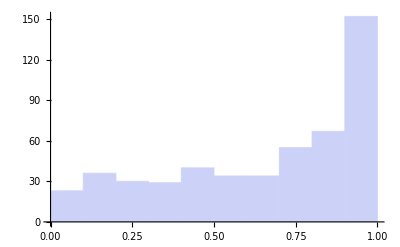

```mathematica
Histogram[RandomReal[BetaDistribution[0.99,0.5],500]]
```

```mathematica
End[]
```

Optimise`ParticleSwarm`Private`

```mathematica
EndPackage[]
```